```mathematica
ClearAll["Global`*"]
```

```mathematica
<<"/Users/alexdeich/thesis/code/mine/ThesisTools.m"
```

#### Calculate force on one particle

G[f_,i_] returns the force on the particle i whose position in state space is given in f , which is an array (created above as InitVecs.)

```mathematica
G[f_,i_]:=Module[{x,y,j,r,P,r1,r2,P1,P2,distance2,jforce,jforcedir,totalforce,forces},
forces = Table[{0.,0.},Nparticles];
r1 = f[[i,1,1]];
P1 = f[[i,1,2]];
For [j=1,j≤ Nparticles,j++,
If[j≠ i,
r2 = f[[j,1,1]];
P2 = f[[j,1,2]];
distance2 = (r1^2+r2^2 - 2r1 r2 (Cos[P1-P2]));
(*If[distance2<epsilon,
Print["Something collided"];
Abort[];
];*)
jforce = 1/distance2;
jforcedir = {,}/Sqrt[distance2];(*CALCULATING DIRECTION WRONG. SWITCHING TO CARTESIAN COORDINATES*)
forces[[j]] = jforce*jforcedir;
];
];
Return[Total[forces]];
]
```

```mathematica
G[InitVecs,1]
```

Power::infy: Infinite expression 1/0. encountered.

{0.0277778,Indeterminate}

```mathematica
InitVecs
```

{{{3.,-1.5708},{0,0}},{{3.,1.5708},{0,0}}}

#### Get force on every particle

GetForces[state_] returns an array with size Nparticles with the force information for each particle in r and P. {{fr},{fP}}

```mathematica
GetForces[state_]:=Module[{particle,totalforces},
totalforces = Table[{},Nparticles];
For[particle=1,particle≤Nparticles,particle++,
totalforces[[particle]]=G[state,particle]
];
Return[totalforces]
]
```

For a sanity check, if Nparticles==2, the two forces returned should be equal and opposite.

```mathematica
forcelist = GetForces[InitVecs]
```

{{0.,0.0145444},{0.,-0.0145444}}

#### Initilialize potentially usefull things

Initialize state vector with {{r,P},{rd,Pd}}

```mathematica
Nparticles = 2;
InitVecs = Table[{{3.,Pi/2.*((-1)^n)},{0,0}},{n,1,Nparticles}];
timesteps = 10000;
dt = .001;
mass = 1;
epsilon = 0.000001;
wholestory = Table[0,timesteps];
```

```mathematica
InitVecs
```

{{{3.,-1.5708},{0,0}},{{3.,1.5708},{0,0}}}

#### Time evolution

```mathematica
StateVecs = InitVecs;
For[timestep = 1,timestep≤timesteps,timestep++,
currentforces = GetForces[StateVecs];
NewState = Table[{{0,0},{0,0}},Nparticles];
For[i=1,i≤ Nparticles,i++,
oldr = StateVecs[[i,1,1]];
oldP = StateVecs[[i,1,2]];
oldrd = StateVecs[[i,2,1]];
oldPd = StateVecs[[i,2,2]];
rdd= currentforces[[i,1]]/mass;
Pdd = currentforces[[i,2]]/mass;
newr = oldrd * dt + oldr;
newP = oldPd * dt + oldP;
newrd = rdd*dt + oldrd;
newPd = Pdd*dt + oldPd;
NewState[[i]][[1,1]] = newr;
NewState[[i]][[1,2]] = newP;
NewState[[i]][[2,1]] = newrd;
NewState[[i]][[2,2]] = newPd;
];
StateVecs = NewState;
(*Print[timestep," ",StateVecs];*)
wholestory[[timestep]] = StateVecs;
]
```

```mathematica
wholestory
```

{{{{3.,-1.5708},{0.,0.0000145444}},{{3.,1.5708},{0.,-0.0000145444}}},9998,{{{3.,-0.866208},{0.,0.142948}},{{3.,0.866208},{0.,-0.142948}}}}
 |  |  |  |

#### Plotting

```mathematica
colors = {Blue,Red,Orange,Green};
```

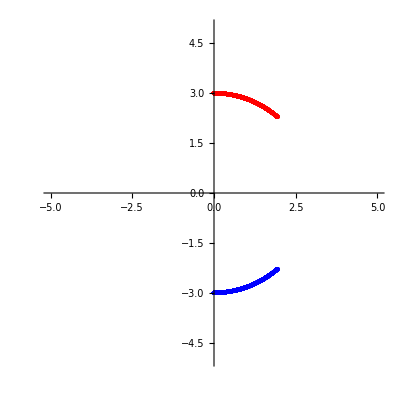

```mathematica
xyplots = Table[0,Nparticles];
For[particle=1,particle≤Nparticles,particle++,
xyplots[[particle]] = ListPolarPlot[Table[{wholestory[[t,particle,1,2]],wholestory[[t,particle,1,1]]},{t,1,timesteps}],PlotRange->{{-5,5},{-5,5}},PlotStyle->{colors[[particle]],PointSize[Large]}];
]
Show[xyplots]
```